```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/FEinterpolants.nb"]
```

```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
```

## mtx

```mathematica
A11=Import["A11.rua"];
B1=Import["B1.rra"];
B2=Import["B2.rra"];
```

```mathematica
A=ArrayFlatten[{{A11,0},{0,A11}}];
B=ArrayFlatten[{{B1,B2}}];
```

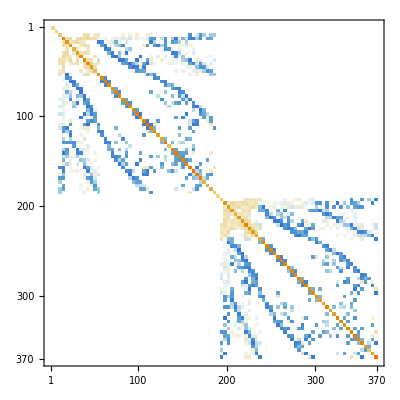

```mathematica
MatrixPlot@A
```

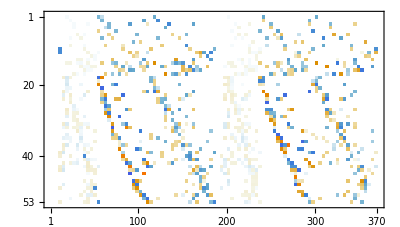

```mathematica
MatrixPlot@B
```

```mathematica
𝒜=ArrayFlatten[{{A,Transpose@B},{B,0}}];
```

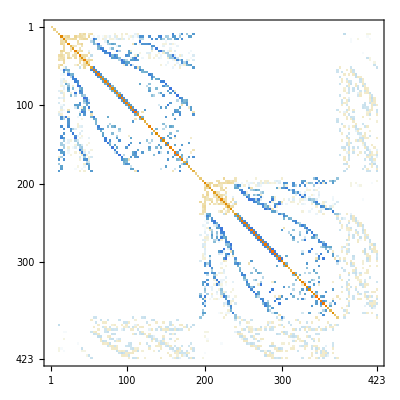

```mathematica
MatrixPlot@𝒜
```

```mathematica
b=Import["b.dat"][[1]];
```

## mtx prop

```mathematica
Det@A
```

1.54411×10^259

```mathematica
A[[30,4]]
```

0.

```mathematica
Det@𝒜
```

-3.34044×10^124

```mathematica
MatrixPlot@B
```

-Graphics-

```mathematica
MatrixRank@B
Length@NullSpace@B
```

53

317

```mathematica
NullSpace@Transpose@B
```

{}

```mathematica
data=Eigenvalues@𝒜
```

Eigenvalues::arh: Because finding 423 out of the 423 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{20.7265,20.7265,20.4532,20.4531,20.3067,20.3066,20.1548,20.1548,20.1416,20.1415,18.6315,18.6314,18.6158,18.6157,18.2806,18.2806,17.9954,17.9954,17.8394,17.8394,17.5364,17.5364,17.4628,17.4628,17.1845,17.1845,16.8797,16.8797,16.7927,16.7927,16.6979,16.6978,16.6351,16.6351,16.4753,16.4753,16.2686,16.2685,16.0463,16.0462,15.9919,15.9919,15.898,15.8979,15.7144,15.7144,15.6787,15.6787,15.4834,15.4833,15.2974,15.2973,15.2349,15.2348,15.1371,15.1371,15.0236,15.0236,14.8856,14.8855,14.4787,14.4787,14.4066,14.4066,14.2868,14.2868,14.1482,14.1482,14.0544,14.0544,13.9289,13.9289,13.7605,13.7604,13.6695,13.6695,13.5917,13.5917,13.4736,13.4735,13.1919,13.1919,13.1641,13.1641,13.0217,13.0216,12.9469,12.9468,12.8118,12.8117,12.6318,12.6317,12.446,12.4459,12.3074,12.3073,12.2087,12.2085,12.1345,12.1343,12.0563,12.0562,11.9992,11.9992,11.8654,11.8653,11.7825,11.7824,11.6582,11.6582,11.5148,11.5148,11.3789,11.3787,11.3145,11.3143,11.2509,11.2509,11.0971,11.0971,11.0111,11.011,10.9839,10.9839,10.8506,10.8505,10.8161,10.8159,10.7582,10.7581,10.6885,10.6883,10.6569,10.6568,10.5281,10.5277,10.4723,10.472,10.4343,10.4339,10.3823,10.382,10.3185,10.3184,10.1721,10.1718,9.98281,9.98268,9.89967,9.89959,9.82017,9.8201,9.69478,9.69449,9.50966,9.50925,9.44058,9.44041,9.41656,9.41639,9.20894,9.20859,9.07689,9.07647,8.79911,8.79869,8.76206,8.76178,8.69345,8.69312,8.60356,8.60354,8.49425,8.49406,8.46148,8.46137,8.36307,8.36293,8.12294,8.12221,8.10845,8.10772,7.92374,7.92315,7.90077,7.90068,7.83135,7.83113,7.74093,7.74061,7.6539,7.65327,7.50577,7.50543,7.46306,7.46283,7.32576,7.32496,7.29156,7.29115,6.92971,6.92944,6.77586,6.77508,6.71197,6.71125,6.53248,6.53188,6.36771,6.36757,6.17068,6.17026,5.8764,5.8759,5.7777,5.77685,5.74654,5.74619,5.56762,5.56731,5.28868,5.28847,4.91851,4.91838,4.82152,4.8213,4.65346,4.65331,4.3742,4.37399,4.32504,4.32483,4.22753,4.22689,4.20104,4.20082,4.11161,4.11045,3.96096,3.96057,3.76196,3.76144,3.68498,3.68462,3.50253,3.50215,3.44633,3.44575,3.33464,3.33369,3.16955,3.16882,3.13792,3.13564,3.02453,3.02361,2.93659,2.93597,2.88554,2.88307,2.63659,2.63491,2.36753,2.36666,2.32349,2.32157,2.26573,2.26285,2.08108,2.08071,2.03164,2.02866,1.77063,1.76849,1.68798,1.68701,1.55712,1.55534,1.50503,1.50025,1.2818,1.2787,1.16419,1.16193,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.988444,0.984618,0.83566,0.829542,0.737338,0.735606,0.501748,0.495994,0.392962,0.388715,0.171699,0.167412,-0.011191,-0.0107788,-0.00864578,-0.00830212,-0.00815499,-0.00745114,-0.00736004,-0.00713178,-0.00696388,-0.00657007,-0.00612056,-0.00595808,-0.00583376,-0.0054839,-0.00517564,-0.0049709,-0.00474727,-0.00454707,-0.00435993,-0.00435358,-0.00419972,-0.00400217,-0.0039622,-0.00385646,-0.00366745,-0.003565,-0.00320551,-0.00313134,-0.00307515,-0.00295056,-0.00271927,-0.00261124,-0.00257842,-0.00247419,-0.00233561,-0.00213705,-0.00203189,-0.00182866,-0.00172493,-0.00167953,-0.00158571,-0.00146519,-0.00123685,-0.0011818,-0.00114338,-0.00104028,-0.000995509,-0.000910793,-0.000669164,-0.000637047,-0.000621834,-0.000410343,-0.000397822}

```mathematica
Sort[Norm/@data];
```

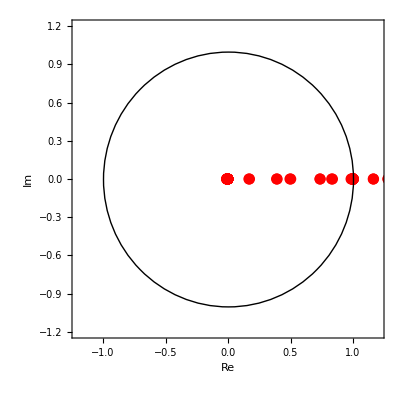

```mathematica
spplot=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];

Show[spplot,Graphics@Circle[{0,0},1]]
```

## soln

```mathematica
z=LinearSolve[𝒜,b,Method->{Krylov,Method->BiCGSTAB}];
```

```mathematica
n=Length@A;
vel1=z[[;;n/2]];
vel2=z[[n/2+1;;n]];
velmag=Table[Norm[{vel1[[i]],vel2[[i]]}],{i,Length@vel1}];
pre=z[[n+1;;]];
```

```mathematica
𝒯=import["mesh.ntr"];
highlight[𝒯,{"nodesNumn","ribsNumn","trianglesNumn"}]
```

-Graphics-

```mathematica
pressureFE=ΔP1L;
velocityFE=ΔP2L;
```

```mathematica
ph=𝒫[pre,pressureFE,𝒯];
(*pplot=plot𝒫ξ[ph,𝒯];*)
```

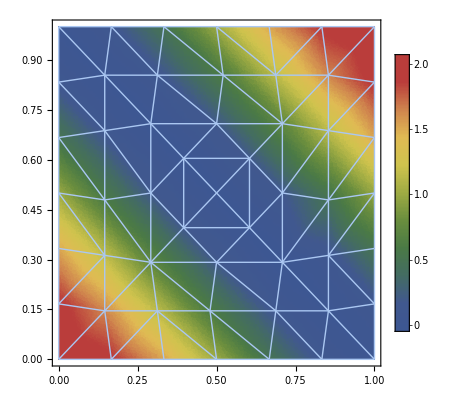

```mathematica
densityPlot𝒫ξ[ph,𝒯,{Min@pre,Max@pre},"DarkRainbow",True]
```

```mathematica
Show[Plot3D[Subscript[p, 0][x,y],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],pplot,ImageSize->Medium]
```

-Graphics3D-

```mathematica
computeErrorNorm[Subscript[p, 0],ph,𝒯]
```

0.0132332

```mathematica
v1h=𝒫[vel1,velocityFE,𝒯];
v2h=𝒫[vel2,velocityFE,𝒯];
velmagh=𝒫[velmag,velocityFE,𝒯];
```

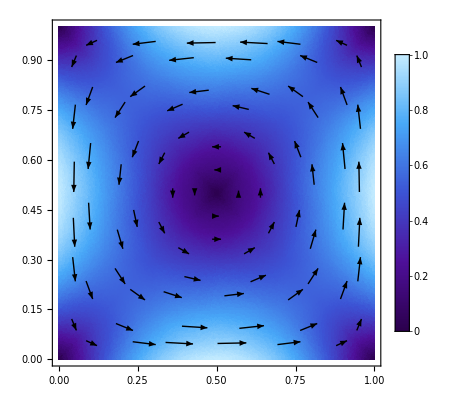

```mathematica
Show[densityPlot𝒫ξ[velmagh,𝒯,{Min@velmag,Max@velmag},"DeepSeaColors",False],vectorPlot𝒫ξand𝒫η[v1h,v2h,𝒯]]
```

```mathematica
v1plot=plot𝒫ξ[v1h,𝒯];
v2plot=plot𝒫ξ[v2h,𝒯];
```

```mathematica
Show[Plot3D[u[x,y][[1]],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],v1plot,ImageSize->Medium]
Show[Plot3D[u[x,y][[2]],{x,y}∈Ω,Mesh->None,PlotStyle->LightBlue],v2plot,ImageSize->Medium]
```